```mathematica
FileExport[data_, filename_?StringQ, parser_?StringQ] :=
With[
{folder=FileNameJoin[{ParentDirectory@NotebookDirectory[], "LaTeX", "pic"}]},
If[FileType[folder]== None,CreateDirectory[folder]];
Export[FileNameJoin[{folder,filename}] , data, parser];
];
```

```mathematica
(*Исходные данные*)
EE=1;(*2.1*10^11;*)
d=10/1000;
J=1;(*Pi*d^4/64;*)
l=1;
t0 = -1*Pi/180;
u0 = 0; (*заданное перемещение левого края*)
uk = 0; (*заданное перемещение правого края*)
tk=0;
q =-1; (*интенсивность распределенной нагрузки Н/м*)
z0=3*l/7;
StifMtr[l_,EE_,J_]:=EE*J/l^3*{{12,6*l,-12,6*l},{6*l,4*l^2,-6*l,2*l^2},{-12,-6*l,12,-6*l},{6*l,2*l^2,-6*l,4*l^2}};
KglobStiff[n_,AllLength_,Emodule_,J_]:=Module[{Kglob},
Kglob=Table[0,{i,1,(n+1)*2},{j,1,(n+1)*2}];
Do[
Do[
    Do[
        Kglob[[i+2*(count-1),j+2*(count-1)]]+=StifMtr[AllLength/n,Emodule,J][[i,j]],
       {j,1,4}
       ],
   {i,1,4}
  ],
{count, 1,n}
];
Kglob
];

SolvingModuleFEM[n_,l_,EE_,J_,q_]:=Module[{Kstiff,ForceVec,NumOfDOF,Lelem,DispVec,sol,ElemLoad,loadLoc,tmpLoad,f1,f2,f3,f4,count},
loadLoc[z_,zStart_]:=If[z+zStart≤z0,q*Sin[Pi*(z+zStart)/z0],q*Sin[Pi*((z+zStart)-z0)/z0]];(*If[z+zStart≤8/10*z0,q*Sin[Pi*(z+zStart)/z0],q*Sin[Pi*((z+zStart)-z0)/z0]]*);
f1[z_,Lelem_]:=1-(3 z^2)/Lelem^2+(2 z^3)/Lelem^3;
f2[z_,Lelem_]:=z-(2 z^2)/Lelem+z^3/Lelem^2;
f3[z_,Lelem_]:=(3 z^2)/Lelem^2-(2 z^3)/Lelem^3;

f4[z_,Lelem_]:=-z^2/Lelem+z^3/Lelem^2;
count = 3;
NumOfDOF=(n+1)*2;
Lelem=l/n;
Kstiff=Table[0,{i,1,NumOfDOF},{j,1,NumOfDOF}];
Kstiff=KglobStiff[n,l,EE,J];
tmpLoad={};
ForceVec=Table[0,{i,1,NumOfDOF}];
(*добавление распределенной нагрузки по всей длине*)
ElemLoad [zStart_]:=NIntegrate[loadLoc[z,zStart]*{f1[z,Lelem],f2[z,Lelem],f3[z,Lelem],f4[z,Lelem]},{z,0,Lelem},WorkingPrecision->17,AccuracyGoal->15,PrecisionGoal->15];
Do[
AppendTo[tmpLoad,ElemLoad [(i-1)*Lelem]],
{i,1,n,1}
];
(*Print[tmpLoad];*)
tmpLoad=Flatten[tmpLoad];
Do[
ForceVec[[count]]=tmpLoad[[j]]+tmpLoad[[j+2]];
ForceVec[[count+1]]=tmpLoad[[j+1]]+tmpLoad[[j+1+2]];
count = count +2,
{j,3,Length[tmpLoad]-2,4}
];
ForceVec[[1]]=tmpLoad[[1]];
ForceVec[[2]]=tmpLoad[[2]];
ForceVec[[-1]]=tmpLoad[[-1]];
ForceVec[[-2]]=tmpLoad[[-2]];
(*Print[ForceVec];*)
(*заготовка вектора перемещений в виде некоторых неизвестных*)
DispVec=Table[u[i],{i,1,NumOfDOF}];
(*Учёт кинематических граничных условий*)
ForceVec=ForceVec-Kstiff[[All,1]]*u0-Kstiff[[All,-2]]*uk-Kstiff[[All,2]]*t0-Kstiff[[All,-1]]*tk; (*коррекция вектора узловых сил для учета поворота в заделке, чтобы использовать метод крестика для учета ГУ*)
ForceVec[[1]]=u0; (*коррекция вектора узловых усилий, чтобы перемещение слева было u0*)
ForceVec[[2]]=t0;
ForceVec[[-1]]=tk;
ForceVec[[-2]]=uk; (*коррекция вектора узловых усилий, чтобы перемещение справа было uк*)
Kstiff[[1;;2,All]]=0;
Kstiff[[All,1;;2]]=0;
Kstiff[[1,1]]=1;
Kstiff[[2,2]]=1;
Kstiff[[-2;;-1,All]]=0;
Kstiff[[All,-2;;-1]]=0;
Kstiff[[-2,-2]]=1;
Kstiff[[-1,-1]]=1;
sol=NSolve[Kstiff.DispVec==ForceVec,DispVec]//First;
DispVec=Evaluate[DispVec/.sol]
]

PrecisionSol[l_,EE_,J_,q_]:=Module[{Sys,solPrec,tmp},
Sys=
{
EE*J*y''''[z]==If[z≤z0,q*Sin[Pi*z/z0],q*Sin[Pi*(z-z0)/z0]],
y[0]==u0,
y'[0]==t0,
y[l]==uk,
y'[l]==tk
};
solPrec=DSolve[Sys,y[z],z]//First;
Print[solPrec];
tmp=Evaluate[y[z]/.solPrec]
]
```

{y[z]→1/(432180 π^4)(34020 π z-2401 π^5 z-21870 √3 z^2-99630 π z^2-25920 π^3 z^2+4802 π^5 z^2+14580 √3 z^3+26730 π z^3+37440 π^3 z^3-2401 π^5 z^3+432180 π^4 (Piecewise[{{-(81 Sin[(7 π z)/3])/(2401 π^4), z≤3/7}, {-162/(2401 π^3)+(3 (1/21 π^2 (3-7 z)^3+18 z+(27 Sin[(7 π z)/3])/(7 π)))/(343 π^3), True}}]))}

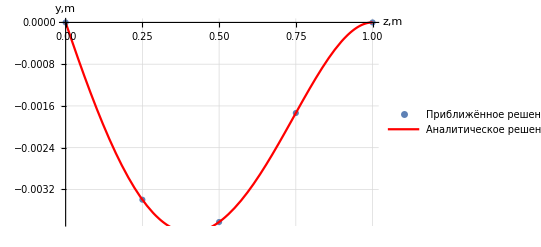

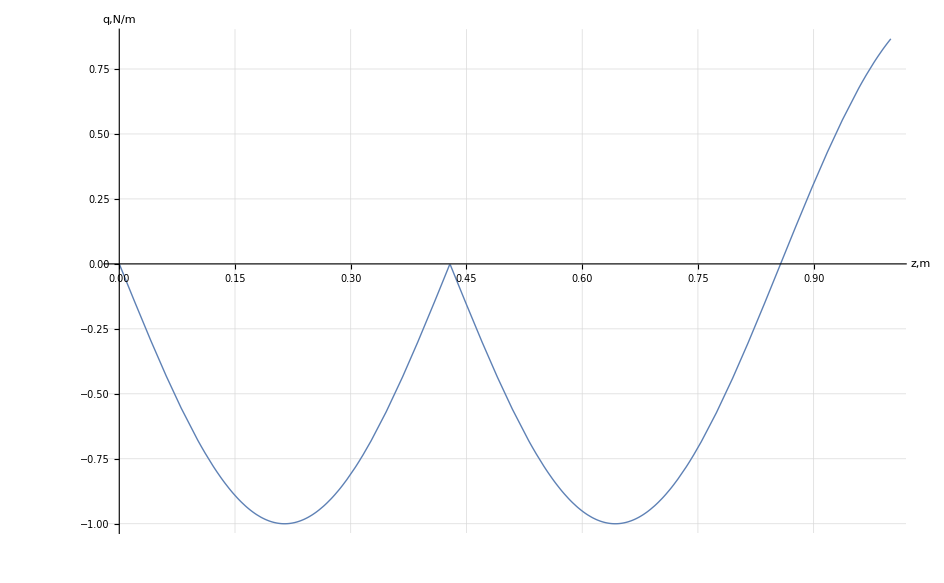

```mathematica
NElem=4;
UFEM=SolvingModuleFEM[NElem,l,EE,J,q];
yFEM=Table[{l/NElem*(i-1)/2,UFEM[[i]]},{i,1,(NElem+1)*2,2}];
yfunc=PrecisionSol[l,EE,J,q];
pic1=ListPlot[yFEM,GridLines->Automatic,PlotMarkers->Automatic,AxesStyle->32,AxesLabel->{"z,m","y,m"},PlotRange->All,PlotLegends-> {"Приближённое решение"},LabelStyle->Directive[Black,Large]];
pic2=Plot[yfunc/.z->x,{x,0,l},GridLines->Automatic,AxesStyle->32,AxesLabel->{"z,m","y,m"},PlotStyle->{Thick,Red},PlotLegends-> {"Аналитическое решение"},LabelStyle->Directive[Black,Large]];
Show[pic1,pic2,PlotLegends-> {"Приближённое решение","Аналитическое решение"},LabelStyle->Directive[Black,Large],AxesStyle->32]
Plot[If[z≤z0,q*Sin[Pi*z/z0],q*Sin[Pi*(z-z0)/z0]],{z,0,l},GridLines->Automatic,AxesStyle->32,AxesLabel->{"z,m","q,N/m"},PlotStyle->{Thick},LabelStyle->Directive[Black,Large],AxesStyle->32]
```

(27 z)/(343 π^3)-(π z)/180-(243 √3 z^2)/(4802 π^4)-(1107 z^2)/(4802 π^3)-(144 z^2)/(2401 π)+(π z^2)/90+(81 √3 z^3)/(2401 π^4)+(297 z^3)/(4802 π^3)+(208 z^3)/(2401 π)-(π z^3)/180+(Piecewise[{{-(81 Sin[(7 π z)/3])/(2401 π^4), 7 z≤3}, {(-π (-54+π^2 (3-7 z)^2) (-3+7 z)+81 Sin[(7 π z)/3])/(2401 π^4), True}}])

-0.014915 z+0.0074812 z^2+0.012717 z^3+(Piecewise[{{-0.00034633 Sin[7.3304 z], 7. z≤3.}, {4.2757×10^-6 (-3.1416 (-54.+9.8696 (3.-7. z)^2) (-3.+7. z)+81. Sin[7.3304 z]), True}}])

{2,0.0000570146}

{4,2.99174×10^-6}

{8,2.08056×10^-7}

{16,1.30141×10^-8}

{32,8.11841×10^-10}

{{2,0.0000570146},{4,2.99174×10^-6},{8,2.08056×10^-7},{16,1.30141×10^-8},{32,8.11841×10^-10}}

{2,0.0000570146}

{4,2.99174×10^-6}

{8,2.08056×10^-7}

{16,1.30141×10^-8}

{32,8.11841×10^-10}

{{2,0.0000570146},{4,2.99174×10^-6},{8,2.08056×10^-7},{16,1.30141×10^-8},{32,8.11841×10^-10}}

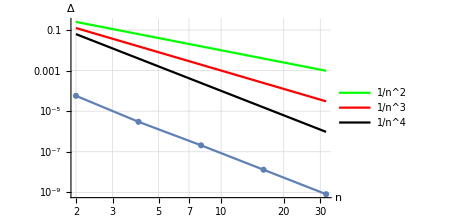

```mathematica
Yt[z_]:=1/(432180 π^4)(34020 π z-2401 π^5 z-21870 √3 z^2-99630 π z^2-25920 π^3 z^2+4802 π^5 z^2+14580 √3 z^3+26730 π z^3+37440 π^3 z^3-2401 π^5 z^3+432180 π^4 (Piecewise[{{-(81 Sin[(7 π z)/3])/(2401 π^4), z≤3/7}, {-162/(2401 π^3)+(3 (1/21 π^2 (3-7 z)^3+18 z+(27 Sin[(7 π z)/3])/(7 π)))/(343 π^3), True}}]));
Expand[FullSimplify[Yt[z]]]
N[Expand[FullSimplify[Yt[z]]],5]
yFEMfunc[l_,nElem_,UFEM_]:=Module[{N1,N2,N3,N4,Lelem,u1,v1,u2,v2},
Lelem=l/nElem;
N1[x1_,x2_,z_]:=Piecewise[{{((z-x2)^2 (2 z-3 x1+x2))/(x2-x1)^3,x1≤z<=x2}},0];    (*Функции Эрмита (стыковочные функции Эрмита)*)
N2[x1_,x2_,z_]:=Piecewise[{{((z-x1) (z-x2)^2)/(x1-x2)^2,x1≤z<=x2}},0];
N3[x1_,x2_,z_]:=Piecewise[{{((z-x1)^2 (2 z+x1-3 x2))/(x1-x2)^3,x1≤z<=x2}},0];
N4[x1_,x2_,z_]:=Piecewise[{{((z-x1)^2 (z-x2))/(x1-x2)^2,x1≤z<=x2}},0];

Sum[ UFEM[[(i-1)*2+1]]*N1[(i-1)*Lelem,(i)*Lelem,z]+UFEM[[(i-1)*2+2]]*N2[(i-1)*Lelem,(i)*Lelem,z]+UFEM[[(i-1)*2+3]]*N3[(i-1)*Lelem,(i)*Lelem,z]+UFEM[[(i-1)*2+4]]*N4[(i-1)*Lelem,(i)*Lelem,z],{i,1,nElem}]
]

ErrorFunc[l_,EE_,J_,q_]:=Module[{UFEM,yFEM,yfunc,listZ,listEr,tmp,listN,listRes,listErPrint,yFEMFromZ,err,Lelem,dz},
listEr={};
listN={};
listErPrint={};
dz = 1/10^4;
Do[
UFEM=SolvingModuleFEM[n,l,EE,J,q];
yFEMFromZ=yFEMfunc[l,n,UFEM];(*Print[yFEMFromZ];*)
(*err=Sum[(Abs[yFEMFromZ-Yt[z]])*dz,{z,0.00001,l,dz}];*)
err = NIntegrate[Sqrt[(yFEMFromZ-Yt[z])^2],{z,0,l}];
Print[{n,err}];
AppendTo[listEr,err];
AppendTo[listErPrint,{n,err}];
AppendTo[listN,n],
{n,{2,4,8,16,32}}
];
Print[listErPrint];
listRes=Table[{listN[[i]],listEr[[i]]},{i,1,Length[listN]}]
]

(*ListPlot[ErrorFunc[l,EE,J,q],PlotMarkers->Automatic,Joined->True,AxesOrigin->{0,0}]*)
s=ErrorFunc[l,EE,J,q];
picErr=ListLogLogPlot[ErrorFunc[l,EE,J,q],
PlotMarkers->Automatic,
Joined->True,
AxesOrigin->{0,0},
AxesLabel->{"n","Δ"},
LabelStyle->Directive[Black,18, FontFamily -> "Times"]
];
picX4=LogLogPlot[{1/x^2,1/x^3,1/x^4},{x,2,32},
PlotStyle->{Green,Red,Black},
PlotLegends->{"1/n^2","1/n^3","1/n^4"},
LabelStyle->Directive[Black,18, FontFamily -> "Times"]
];
output=Show[picErr,picX4,LabelStyle->Directive[Black,18, FontFamily -> "Times"],PlotRange->All, GridLines-> Automatic,ImageSize->350]
FileExport[output, "2_nodebeam_plain.pdf", "PDF"]
```

```mathematica
d
```

1/100

```mathematica
Grid[{
{"N",2,4,8,16, 32},
{"Δ",s[[1,2]],s[[2,2]],s[[3,2]],s[[4,2]], s⟦5,2⟧},{"ω",Abs[Log[2,s[[2,2]]/s[[1,2]]]],Abs[Log[2,s[[3,2]]/s[[2,2]]]],Abs[Log[2,s[[4,2]]/s[[3,2]]]], Abs[Log[2,s[[5,2]]/s[[4,2]]]]}},Frame->All]
```

N | 2 | 4 | 8 | 16 | 32
Δ | 0.0000570146 | 2.99174×10^-6 | 2.08056×10^-7 | 1.30141×10^-8 | 8.11841×10^-10
ω | 4.25227 | 3.84594 | 3.99882 | 4.00274 |